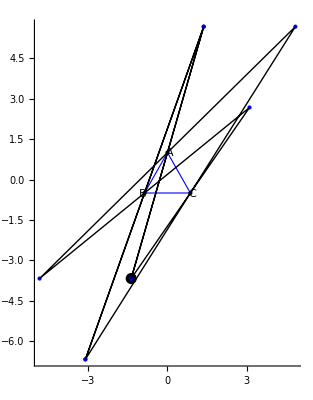

```mathematica
(*Outer Billiard problem*)

(*Author: Evan Huynh, Marcel Vosshans*)
(*Creating a triangle*)
(*Written on Mathematical 11 FrontEnd, for submission*)
(*This might not work on Mathematica 10 or older*)


(*------------Drafted function 1-----------------*)
(*Adapted from: https://stackoverflow.com/questions/3938488/naming-variable-in-mathematica-with-an-algorithm*)
(*Function getNextTrailingNumberInString will take the string with the end variable and plus 1
Ex: getNextTrailingNumberInString["YourName12"] -> "YourName13";
getNextTrailingNumberInString["YourName19"]-> "YourName20";
getNextTrailingNumberInString["YourName99"]-> "YourName100";
If no number found -> Print the string;
If empty string -> Break;
Only works with trailing numbers;
*)
getNextTrailingNumberInString[varNum_?StringQ]:=(
If[varNum=="",Break;,
k=-1;
d=StringTake[varNum,k];
z=NumberQ[ToExpression[d]]]

While[z,
k=k-1;
d=StringTake[varNum,k];
z=NumberQ[ToExpression[d]]];

If[NumberQ[ToExpression[StringTake[varNum,k+1]]],
d=ToExpression[StringTake[d,k+1]]+1;
k=k+1+StringLength[varNum];
StringTake[varNum,k]<>ToString[d],StringTake[varNum,StringLength[varNum]]]
)
(*------------Drafted function 1-----------------*)

(*------------Drafted function 2-----------------*)
(*Adapted from: https://stacoverflow.com/questions/393888/naming-variable-in-mathematica-with-an-algorithm*)
(*Get the last number in string and export it*)
getTrailingNumberInString[varNum_?StringQ]:=(
If[varNum=="",Break,
k=-1;
d=StringTake[varNum,k];
z=NumberQ[ToExpression[d]]]

While[z,
k=k-1;
d=StringTake[varNum,k];
z=NumberQ[ToExpression[d]]];

If[NumberQ[ToExpression[StringTake[varNum,k+1]]],
d=ToExpression[StringTake[d,k+1]];
k=k+1+StringLength[varNum];
StringTake[varNum,k]<>ToString[d],StringTake[varNum,StringLength[varNum]]]
)
(*------------Drafted function 2-----------------*)

(*------------Drafted function 3-----------------*)
(*Create a point of reflection over a middle point*)
(*Usage: reflectPoint[{outPoint},{middlePoint}], point in 2D only
Ex: reflectPoint[{1,2},{2,5}]-> {3,8}
*)
reflectPoint[outPoint_,middlePoint_]:=(
xMove = -(outPoint[[1]]-middlePoint[[1]]);
yMove=-(outPoint[[2]]-middlePoint[[2]]);
{middlePoint[[1]]+xMove,middlePoint[[2]]+yMove}
)
(*------------Drafted function 3-----------------*)

(*End of drafted functions*)

(*-------------BEGIN---------------*)
(*Create the first equilateral triangle*)
triangle1={Polygon[CirclePoints[3]]};
xC=(√3)/2; yC=-1/2;
pointB={xB,yB};
xA=0;yA=1;
pointA={xA,yA};
xB=-(√3)/2;yB=-1/2;
pointC={xC,yC};

(*Mapping points and labeling it*)
textA= Text["A",{0.1,1}];
textC = Text["C",{0.92,-0.54}];
textB = Text ["B",{-0.92,-0.54}];

(*Creating a point K randomly and check if it is in the triangle*)

xK=RandomReal[{-4,4}];yK=RandomReal[{-4,4}];

While[(xB<xK<xC)||(yB<yK<yA),
xK=RandomReal[{-4,4}];yK=RandomReal[{-4,4}];
]


pointK={xK,yK};
(*textK=Text["K",{-1.05,1.53}];*)

pointList={pointK};

(*Add everything to the plot2 initially*)
plot2={EdgeForm[Directive[Thick,Blue]],Directive[White],triangle1,Directive[Black],Point[pointA],Point[pointB],Point[pointC],textA,textB,textC,PointSize[0.02],Point[pointK]};
(*Done creating a equilateral triangle*)

(*Add point to list*)
doCtimes=RandomInteger[{1,10}];
Do[
If[Mod[Length[pointList],3]==1,
pointList=AppendTo[pointList,reflectPoint[Last[pointList],pointA]];,
If [Mod[Length[pointList],3]==2,
pointList=AppendTo[pointList,reflectPoint[Last[pointList],pointB]];,
pointList=AppendTo[pointList,reflectPoint[Last[pointList],pointC]];
]
]
,doCtimes];

plot3={Blue,Point[pointList],Black,Line[pointList]};

plot4 = {plot2,plot3};

(*Export the result*)
Show[Graphics[{plot4}],Axes-> True,AxesStyle->Black]
(*-----------------*)

(*--------------END----------------*)
```